Here it is evaluated the noise in a cell colony where each cell expresses a self-regulated gene. The cells are connected by diffusion of the genetic product (i.e. paracrine signal). In each cell, the regulatory system is represented two Chemical Langeving Equations (CLE).  One for mRNA expression and the other one for protein expression according to Yan et al 2017.

```mathematica
SetDirectory[]
```

## Parameters

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
radius=15; (* Coloby cell radius *)
iteraciones=1000; (* Number of algorithm iterations. An error could be get if there is less than 500 iterations *)
replicas=2;  (* Number of times the algorithm is run *)

name=0.009;   (* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.02];
γgs=Range[0.02,2,0.04]; (* subRanges: 0.02-0.18, 0.22-0.38, 0.42-0.58, 0.62-0.78, 0.82-0.98, 1.02-1.18, 1.22-1.38, 1.42-1.58, 1.62-1.78, 1.82-1.98 *)
γms=Range[0.001,0.1,0.002];(* subRanges: 0.001-0.009, 0.011-0.019, 0.021-0.029, 0.031-0.039, 0.041-0.049, 0.051-0.059, 0.061-0.069, 0.071-0.079, 0.081-0.089, 0.091-0.099 *)
γps=Range[0.001,name,0.002];(* subRanges: 0.001-0.009, 0.011-0.019, 0.021-0.029, 0.031-0.039,0.041-0.049, 0.051-0.059, 0.061-0.069, 0.071-0.079,0.081-0.089, 0.091-0.099 *)
dfs=Range[0.01,0.1,0.01]; (* range values for diffussion coeficient*)

(* variables to name the output data*)
size="default1_"<>ToString[radius];
para1="kon: ";
para1v=kg;
para2=" koff: ";
para2v=γg;
parametro1="_γm";
parametro2="_γp";(* Poner aqui el segundo parametro. Con este se nombra el archivo de salida*)
(*NOTA: Para hacer las graficas se debe ir a cambiar los parametros en abajo*)
```

```mathematica
LaunchKernels[8]
dtGifs=10; 
ventanas=4;
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
Clear[kg,γg,bm,km,γm,kp,γp,τ,ϵ,g,nc];
(*************************TO VARIATE THE REGIONS OF EXPRESSION*)
kg=0.1;(* Gene activation rate (t^-1)*)
γg=0.06;(* Gene desactivation rate (t^-1) *)
(*************************PARAMETERS DEFAULT*)
km=0.696;(* Production rate of mRNA (molecules*t^-1) *)
γm=0.02082;(* Degradation rate (molecules*t^-1) *)
kp=1.386;(* Production rate of proteins (molecules*t^-1) *)
γp=0.02082 ;(* Degradation rate (molecules*t^-1) *)
bp=kp/γm;(* Burst size mean (molecules-protein) *)
bm=km/(γg+kg);(* Burst size mean (molecules-mRNA) *)
kaa=γg/kg; (* Michaelis-Mente constant *)
df=0.01;(* pixeles/minuto , como en Muller 0.7μm2/s*)
h=3; (* Hill's constant *)
dfs=0.01;(* diffusion coeficient: pixeles/minuto , as in Muller 0.7μm2/s*)
ϵ=0.03; (* First control parameter_ the change in the propensity function or in the number of molecules in a step τ is bounded by this number *)
g={1};(* Highest order of reaction in which specie i appears as a reactant, for these cases production and degradation are the Fisrt Order*)
nc=10; (* second control parameters_ indicates the maximum number of fires for a reaction be considered as a critical one *)
species:={mRNA,protein}; (* The values of these are changing in each step τ*)
```

```mathematica
(* NOTA IMPORTANTE: kp y γp no pueden ser exactamente iguales *)
```

## Functions

```mathematica
numero=0.01;  (* Basal transcription *)
autoActivation[activator_,γg_,kg_,h_]:=(activator^h/((γg/kg)+activator ^h));(* self-regulation function *)
ff1[dato_]:=N[Variance[dato]/Mean[dato]];  (* FF for noise meadure *)
expressionNoise[data_]:=N[Variance[data]/Mean[data]^2](* CV2 for noise meadure *)
```

```mathematica
(* CLE for mRNA expression*)equmRNA[mRNA_,bm_,kg_,γm_,regulation_,τ_]:=Module[{rnd1=RandomVariate[NormalDistribution[0,1]],rnd2=RandomVariate[NormalDistribution[0,1]],mRNAs},mRNAs=mRNA+(kg τ bm regulation+(kg τ bm (2 bm + 1)regulation)^(1/2) rnd1 )-(γm mRNA τ+(γm mRNA τ)^(1/2)   rnd2); If[mRNAs>0,mRNAs,numero]];

(* CLE for protein expression*)equProtein[entradaDif_,protein_,mRNA_,kp_,γp_,df_,τ_]:=Module[{rnd1=RandomVariate[NormalDistribution[0,1]],rnd2=RandomVariate[NormalDistribution[0,1]],proteins},proteins=entradaDif*τ+protein+(kp τ mRNA+(kp τ mRNA)^(1/2) rnd1 )-(γp protein τ+(γp protein τ)^(1/2)  rnd2)-df protein *τ; If[proteins>0,proteins,numero]];

(* Algorithm to select τ or Δt *)
τChoicee[mRNA_,protein_,regulation_,kg_,bm_,γm_,kp_,γp_]:=Module[{allμvarNC,τ1,mRNAi,proteini},
mRNAi=If[mRNA==0,numero,mRNA];
proteini=If[protein==0,numero,protein];
(* reactionsVandPF={{{1,kg*bm},{-1,γm*mRNAi}},{{1,kp*proteini},{-1,γp*proteini}}}For each specie introduce the state change value (v) and the propensity (PF) of synthesis and degradation reactions: {{v,PF}-synthesis,{v,PF}-degradation}-specie *);
allμvarNC={{mRNAi,kg*bm*regulation,kg*bm*regulation},{mRNAi,-γm*mRNAi,γm*mRNAi},{proteini,kp*mRNAi,kp*mRNAi},{proteini,-γp*proteini,γp*proteini}};
τ1={Sequence@@Table[Min[Max[ϵ i[[1]]/g,1]/Abs[i[[2]] ],Max[ϵ i[[1]]/g,1]^2/i[[3]] ],{i,allμvarNC[[1;;2]]}],Min[Max[ϵ proteini/g,1]/Abs[Total[allμvarNC[[3;;4,2]]] ],Max[ϵ proteini/g,1]^2/Total[allμvarNC[[3;;4,3]]]]};(*ESTO SALE DEL ARTÍCULO DE Cao 2016 y CHING-YAN 2017. Para cada especie se calcula el tao. Cuando ambas reacciones son no-crticas este se calcula con la suma de la media y la varianza de ambas reacciones. Cuando la degradación se torna critica estas se separan. Cuando hay burst se calcula una tipo de tao para el burst y otro para la degradación (uno cuando es no-critica y otro cuando es critica) *)
Min[τ1[[1]],
If[mRNAi>=10,τ1[[2]],1/(γm*mRNAi) Log[1/(1-RandomReal[{0,1}])]] (*ESTO SALE DEL ARTÍCULO DE Cao 2016*),
If[proteini>=10,τ1[[3]],Sequence@@{Min[Max[ϵ proteini/g,1]/Abs[allμvarNC[[3,2]]],Max[ϵ proteini/g,1]^2/allμvarNC[[3,3]]],1/(γp*proteini) Log[1/(1-RandomReal[{0,1}])]}]]]
```

```mathematica
(* This function gives  the new abundance of cells expressing the self-regulated system and the τ *)newAbundanceUnos[kg_,γg_,bm_,γm_,kp_,γp_,h_,abundancia_,entradaDiff_,df_]:=Module[{τ,mRNA,protein},
τ=τChoicee[abundancia[[1]](*mRNA*),abundancia[[2]](*protein*),autoActivation[abundancia[[2]](*protein*),γg,kg,h],kg,bm,γm,kp,γp];mRNA=equmRNA[abundancia[[1]](*mRNA*),bm,kg,γm,autoActivation[abundancia[[2]](*protein*),γg,kg,h],τ];
protein=equProtein[entradaDiff,abundancia[[2]](*protein*),abundancia[[1]](*mRNA*),kp,γp,df,τ];{{mRNA,protein},τ}]
```

```mathematica
(* This function gives  the new abundance of cells non-expressing the self-regulated system (border cells) *)newAbundanceCeros[abundancia_,entradaDiff_,df_,kp_]:=Module[{abundancia0=abundancia},
abundancia0[[2]]=abundancia0[[2]]+entradaDiff-df*abundancia0[[2]]-kp*abundancia0[[2]];
abundancia0]
newAbundanceCeros2[abundancia_,entradaDiff_,df_,kp_]:=Module[{abundancia0=abundancia},
abundancia0[[2]]=abundancia0[[2]]+entradaDiff-df*abundancia0[[2]]-kp*abundancia0[[2]];
{abundancia0,0}]
```

```mathematica
(* This is the algorithm to estimate the Steady State start from Kelly and Hedengren 2013. It gives the FF since the position estimated as the start of the steady-sate *)ffs[data_]:=Module[{first,ff,n,ffPorVentana,mPorVentana,μ,sd,probabilidades,posicion},
first=Position[data,{__,x_,__}/;x>0][[1,1]];
ff=Table[N[Variance[Flatten[data[[i]]]]/Mean[Flatten[data[[i]]]]],{i,first,data//Length}];
n=(ff//Length)/ventanas;
ffPorVentana=Partition[ff,n];
mPorVentana=Map[Mean,Map[#[[2;;All]]-#[[1;;-2]]&,ffPorVentana](*diferencias por ventana*)];
μ=Table[(1/n)(Total[ffPorVentana[[i]]]-mPorVentana[[i]]*Total[Range[1,n](*tPorVentana*)]),{i,ventanas}];
sd=Table[Sqrt[(1/(n-2))*Sum[(ffPorVentana[[i,j]]-mPorVentana[[i]]*j-μ[[i]])^2,{j,1,Length[ffPorVentana[[i]]]}]],{i,ventanas}];
probabilidades=Map[Total[#]/n&,Table[If[Abs[ffPorVentana[[i,j]]-μ[[i]]]<=sd[[i]],1,0],{i,ventanas},{j,1,n}]]//N;
posicion=((Position[probabilidades,x_/;x>0.1][[1,1]]-1)*n)+1;{ff[[posicion(*con este optengo la posicion a paritir de la cual considerar el ff como en el estado estable*);;All]],posicion}];
```

```mathematica
(* This is the algorithm to estimate the Steady State start from Kelly and Hedengren 2013 *)posicionF[data_]:=Module[{first,ff,n,ffPorVentana,mPorVentana,μ,sd,probabilidades,posicion},
first=Position[data,{__,x_,__}/;x>0][[1,1]];
ff=Table[N[Variance[Flatten[data[[i]]]]/Mean[Flatten[data[[i]]]]],{i,first,data//Length}];
n=(ff//Length)/ventanas;
ffPorVentana=Partition[ff,n];
mPorVentana=Map[Mean,Map[#[[2;;All]]-#[[1;;-2]]&,ffPorVentana](*diferencias por ventana*)];
μ=Table[(1/n)(Total[ffPorVentana[[i]]]-mPorVentana[[i]]*Total[Range[1,n](*tPorVentana*)]),{i,ventanas}];
sd=Table[Sqrt[(1/(n-2))*Sum[(ffPorVentana[[i,j]]-mPorVentana[[i]]*j-μ[[i]])^2,{j,1,Length[ffPorVentana[[i]]]}]],{i,ventanas}];
probabilidades=Map[Total[#]/n&,Table[If[Abs[ffPorVentana[[i,j]]-μ[[i]]]<=sd[[i]],1,0],{i,ventanas},{j,1,n}]]//N;
posicion=((Position[probabilidades,x_/;x>0.1][[1,1]]-1)*n)+1];
```

```mathematica
(* With this function the mean and sd of the FFs are calculated for each of the cells of the colony and in the stable state *)msdFFbyCell[data_,posicion_]:=Module[{ffPorCelulaTodoT,disffPorCelulaTodoT},
ffPorCelulaTodoT=Map[ff1[#]&,Transpose[data][[All,posicion;;All]]];
disffPorCelulaTodoT=FindDistribution[ffPorCelulaTodoT,1,"AIC"][[1,1]];
{Mean[disffPorCelulaTodoT],StandardDeviation[disffPorCelulaTodoT]}]
```

```mathematica
(* With this function we calculate the mean of the mean and the sd of the number of molecules for all cells in each unit of time within the stable state *)
MeanMolecules[data_,posicion_]:=Mean[Map[Mean[#]&,data[[posicion;;All]]]]
```

```mathematica
(*With this function the entropy of the FFs of each circle is calculated in time within the steady state*)FFbyCirculoModuleF[resultados_,matrixCirculos_,posicion_]:=Module[{ffCirculoTiempo,meanFFCirculo},
ffCirculoTiempo=Table[Map[ff1[Pick[#,matrixCirculos,i]]&,resultados[[All,1]][[All,All,2]]],{i,radius}];
Round@Map[Mean,ffCirculoTiempo[[All,posicion;;All]]]
(*Esto es exactamente la Entropia de Shannon en base 10*)]
```

```mathematica
(* This gives the mean ±  SD of some data *)meanSd[datos_]:=Transpose@Map[Through[{Around[Mean@#,StandardDeviation@#]&}@#]&]@Map[Flatten,Transpose[datos]];
```

```mathematica
solucion2D[step_,protein_,comunidadEstadolistTiempos_]:=Module[{celulasValue},
celulasValue=MapThread[#1-> #2&,{Flatten[Pick[matrixPos,matrix,1],1],comunidadEstadolistTiempos[[step,All,protein]]}];
ReplacePart[matrix,celulasValue]];(* To get the graphics *)
```

```mathematica
plot2DF[resultados_]:=Module[{colonyStateTime1,maxprotein},
colonyStateTime1=resultados[[All,1]][[All,posicionUnos]];
maxprotein=Max[Flatten[colonyStateTime1[[All,All,2]]]];
Table[ArrayPlot[solucion2D[i,2,colonyStateTime1],ColorFunctionScaling->False,PlotLegends->Automatic,PlotLabel->"protein molecules, step: "<>ToString[i],PlotRange->{0,maxprotein}],{i,Range[1,iteraciones,dtGifs]}]]
(* To get the graphics-gifs *)
```

```mathematica
ffCircleAcuTimeF[resultados_,posicion_,radius_]:=Module[{ffCirculoTiempo,moleculesCirculoAcuTime},
ffCirculoTiempo=Table[Map[Pick[#,matrixCirculos,i]&,resultados[[All,1]][[posicion;;All,All,2]]],{i,Reverse@Range[1,radius]}];
moleculesCirculoAcuTime=Table[Transpose[ffCirculoTiempo[[1;;i]]],{i,1,radius}];Table[Map[ff1[Flatten[#]]&,moleculesCirculoAcuTime[[j]]],{j,radius}]]
```

```mathematica
(*Plots the temporal FFs by circles *)plot1F[ffCirculoAcuTime_,par1_,par2_,resultados_]:=ListLinePlot[Transpose[{Accumulate[resultados[[All,2]]],
#}]&/@{ffCirculoAcuTime},Frame-> True,FrameLabel-> {"time (min)","FF steady state"},PlotLabel->para1<>ToString[par1]<>para2<>ToString[par2] ,PlotLegends->Range[1,radius],PlotRange-> All,ImageSize->Medium,PlotStyle->Flatten@Table[RGBColor[r,gr,b],{r,{0.5,1}},{gr,{0.1,0.9,.5}},{b,{0.1,0.8,0.2,0.6,0.4}}]]
```

```mathematica
(*Plots the temporal FFs by circles *)plot1Fotro[ffCirculoAcuTime_,par1_,par2_,times_]:=ListLinePlot[Transpose[{Accumulate[times],#}]&/@ffCirculoAcuTime,Frame-> True,FrameLabel-> {"time (min)","FF steady state"},PlotLabel->para1<>ToString[par1]<>para2<>ToString[par2] ,PlotLegends->Range[1,radius],PlotRange-> All,ImageSize->Medium,PlotStyle->Flatten@Table[RGBColor[r,gr,b],{r,{0.5,1}},{gr,{0.1,0.9,.5}},{b,{0.1,0.8,0.2,0.6,0.4}}]]
```

```mathematica
(*Plots the mean of the temporal FFs by circles *)plot2F[data1_,par1_,par2_]:=ListLinePlot[data1,PlotLabel-> para1<>ToString[par1]<>para2<>ToString[par2] ,Frame->True,FrameLabel->{"Disk number","Mean FF steady state"},PlotRange->All,ImageSize->Medium,PlotStyle->RGBColor[0,0.1,1]]
```

```mathematica
(*Plots the sd of the temporal FFs by circles *)plot3F[data2_,par1_,par2_]:=ListLinePlot[data2,PlotLabel-> "sd FF by acumulate circles from inside to outside \n "<>parametro1<>ToString[par1]<>parametro2<>ToString[par2] ,Frame->True,FrameLabel->{"N° acumulate circle","SD FF steady state"},PlotRange->All,ImageSize->Medium,PlotStyle->RGBColor[0,0.1,.5]]
```

```mathematica
ffCircleAcuQF[ffCirculoAcuTime_]:=Module[{uno},
uno=Table[Select[Flatten[i],Quantile[Flatten[i],{0.1}][[1]]<#<Quantile[Flatten[i],{0.95}][[1]]&],{i,ffCirculoAcuTime}];
{Map[Mean,uno],Map[StandardDeviation,uno]}]
```

```mathematica
meanTempBox[resultados_]:=Module[{times},
times=Range[1,iteraciones,100];
BoxWhiskerChart[resultados[[times,1,All,2]],"Diamond",ChartStyle->RGBColor[0.2,.8,1],
ChartLabels->Placed[Accumulate[resultados[[times,2]]], {{0.5, 0}, {1,1.1}},Rotate[#,Pi/4]&]]]
meanTemp[resultados_]:=ListLinePlot[Transpose[{Accumulate[resultados[[All,2]]],
Map[Mean,resultados[[All,1,All,2]]]}],PlotLabel->para1<>ToString[para1v]<>para2<>ToString[para2v],
PlotRange->{{0,1500},All},Frame->True,FrameLabel->{"Time(min)","Mean molecules"},PlotStyle->RGBColor[0.2,.8,1]]
```

## Colonia

Here it is created the colony and the neighbors of each cell are identified

```mathematica
capaCeros=3;
totalFila=radius*2+1+capaCeros*2;
matrix=Join[Table[Table[0,radius*2+1+capaCeros*2],3],Table[{0,0,0,Sequence@@i,0,0,0},{i,DiskMatrix[radius]}],Table[Table[0,radius*2+1+capaCeros*2],3]];
noSeconsideran=Position[Flatten[matrix],0];
neighbors=Flatten[MapThread[List,Map[RotateRight[matrix,#]&,{{0,0},{1,0},{0,-1},{-1,0},{0,1},{1,-1},{-1,-1},{-1,1},{1,1}}],2],1];
matrixPos=Partition[Tuples[Range[1,totalFila],2],totalFila];
neighborsPos=Flatten[MapThread[List,Map[RotateRight[matrixPos,#]&,{{0,0},{1,0},{0,-1},{-1,0},{0,1},{1,-1},{-1,-1},{-1,1},{1,1}}],2],1][[All,2;;All]];
filas=Flatten[matrixPos,1];
asociasiones1=Map[Association,Replace[neighborsPos,x_->( x-> 1),{2}]](* Each association is the neighboors for each cell *);
asociasiones0=Replace[filas,x_->( x-> 0),{1}]//Association (* Is the default, to put 0 in the matrix where there is not conection-neighboors *);
matrizCompleta=Map[#/.asociasiones0&,Map[filas/.#&,asociasiones1]];
totalEqu=Length[matrizCompleta];
vecinosT=Map[Count[#,1]&,matrizCompleta];(* Todos tiene 8 vecinos porque es *)
prVectorEntradaA=Table["df* colonyStateTime[[-1,"<>ToString[i]<>",2]]/"<>ToString[vecinosT[[i]]],{i,1,totalEqu}];
terminosEntradaA=Table[prVectorEntradaA . matrizCompleta[[i]],{i,Length[prVectorEntradaA]}](*dot product*);
```

## Solution-iteration

```mathematica
(* Esto es la condicion inicial para cada célula de cada una de las especies {mRNA,protein,da0,da1} *)
colonyStateTime={Table[{10,10},totalEqu]};
posicionCeros=Position[Flatten[matrix],0]//Flatten;
posicionUnos=Position[Flatten[matrix],1]//Flatten;posicionesUnoMatrix=DeleteCases[Pick[matrixPos,matrix,1],{}];
posicionesCirculos=Union[Flatten@Table[Replace[Union[Flatten[posicionesUnoMatrix[[{i,-i}]],1],Flatten[posicionesUnoMatrix[[i;;-i,{i,-i}]],1]],x_->(x-> i),{1}] ,{i,radius}],{{radius+capaCeros+1,radius+capaCeros+1}-> 0}];
matrixCirculos=Flatten[ReplacePart[matrix,posicionesCirculos]];
```

```mathematica
Table[
allCell=Range[1,totalEqu];
funcionesCeros=Map[Hold[newAbundanceCeros2[colonyStateTime[[-1,#]],Map[ToExpression,terminosEntradaA[[#]]],df,kp]]&,posicionCeros];
funcionesUnos=Map[Hold[newAbundanceUnos[kg,γg,km/(γg+kg)(*bm*),γm,kp,γp,h,colonyStateTime[[-1,#]],Map[ToExpression,terminosEntradaA[[#]]],df]]&,posicionUnos];
asociacionCeros=MapThread[#1-> #2&,{posicionCeros,funcionesCeros}];
asociacionUnos=MapThread[#1-> #2&,{posicionUnos,funcionesUnos}]//Association;
asociacionCeros=MapThread[#1-> #2&,{posicionCeros,funcionesCeros}]//Association;
funcionesAllCell=(allCell/.asociacionCeros)/.asociacionUnos;
(*ojo*)
DistributeDefinitions[posicionF,msdFFbyCell,MeanMolecules,plot2DF,solucion2D ,ffCircleAcuTimeF,ffs,ff1,radius,posicionUnos,iteraciones,dtGifs,matrixPos,matrix,matrixCirculos,FFbyCirculoModuleF,newAbundanceUnos,newAbundanceCeros,newAbundanceCeros2,kg,γg,km,bm,γm,kp,γp,h,df,colonyStateTime,terminosEntradaA,plot1F,plot2F,plot3F,ffCircleAcuQF];
(*********************************to plots 6 and 7*)

(*ojo*)
ffPorCellReplicas={};
meanMoleculesReplicas={};
ffbyCirculoReplicas={};
meanffbyCirculoQReplicas={};
sdffbyCirculoQReplicas={};

SetSharedVariable[resultadosR,ffPorCellReplicas,meanMoleculesReplicas,ffbyCirculoReplicas,meanffbyCirculoQReplicas,sdffbyCirculoQReplicas];

ParallelDo[
Block[{colonyStateTime,resultados,colonyAndSpeciesState,data,posicion,mFFbyCell,sFFbyCell,meanMolecules,ffCirculoAcuTime,meanffCirculoAcuTimeQ,sdffCirculoAcuTimeQ},
colonyStateTime={Table[{10,10},totalEqu]};
resultados=Table[
colonyAndSpeciesState=Map[ReleaseHold,funcionesAllCell];
colonyStateTime={colonyAndSpeciesState[[All,1]]};
{colonyStateTime[[1]],Max[colonyAndSpeciesState[[All,2]]]}

,iteraciones];

data=resultados[[All,1]][[All,posicionUnos]][[All,All,2]];
posicion=posicionF[data];
{mFFbyCell,sFFbyCell}=msdFFbyCell[data,posicion];
meanMolecules=MeanMolecules[data,posicion];

(*Export["burstmRCLEColony"<>size<>"_plot1_df"<>ToString[df],plot2DF[resultados],"GIF"];*)


ffCirculoAcuTime=ffCircleAcuTimeF[resultados,posicion,radius];
{meanffCirculoAcuTimeQ,sdffCirculoAcuTimeQ}=ffCircleAcuQF[ffCirculoAcuTime];
AppendTo[ffPorCellReplicas,{mFFbyCell,sFFbyCell}];
AppendTo[meanMoleculesReplicas,meanMolecules];
AppendTo[ffbyCirculoReplicas,ffCirculoAcuTime];
AppendTo[meanffbyCirculoQReplicas,meanffCirculoAcuTimeQ];
AppendTo[sdffbyCirculoQReplicas,sdffCirculoAcuTimeQ];
resultadosR=resultados;],

replicas];

{meanFFbyCellrep,sdFFbyCellrep}=Map[Mean,Transpose[ffPorCellReplicas]];
meanMoleculesrep=Mean[Flatten[meanMoleculesReplicas]];
meanEntoripasRep=Mean[Map[N@Entropy[Round[#]]&,meanffbyCirculoQReplicas]];
meanRepFFByCircle=Map[Mean,Transpose[meanffbyCirculoQReplicas]];




,{df,{0.01}}];
```

```mathematica
Clear[resultadosR]
```

```mathematica
(*Plots the temporal FFs by circles *)plot1F[ffCirculoAcuTime_,par1_,par2_,resultados_]:=ListLinePlot[Transpose[{Accumulate[resultados[[All,2]]],
#}]&/@{ffCirculoAcuTime},Frame-> True,FrameLabel-> {"time (min)","FF steady state"},PlotLabel->para1<>ToString[par1]<>para2<>ToString[par2] ,PlotLegends->Range[1,radius],PlotRange-> All,ImageSize->Medium,PlotStyle->{Green,Yellow,Red,Blue,Pink}]
```

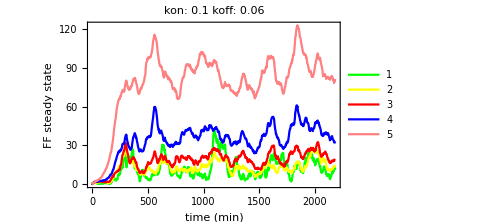

```mathematica
plot1F[ffbyCirculoReplicas[[1]],para1v,para2v,resultadosR]
```

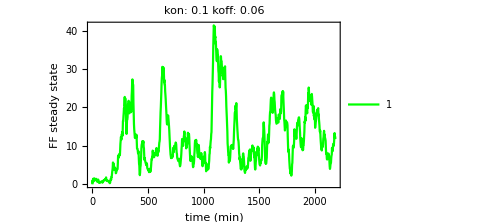

```mathematica
plot1F[ffbyCirculoReplicas[[1,1]],para1v,para2v,resultadosR]
```

```mathematica
(************************************************************************************)
```

```mathematica
dtGifs=50;
```

```mathematica
solucion2D[step_,protein_,comunidadEstadolistTiempos_]:=Module[{celulasValue},
celulasValue=MapThread[#1-> #2&,{Flatten[Pick[matrixPos,matrix,1],1],comunidadEstadolistTiempos[[step,All,protein]]}];
ReplacePart[matrix,celulasValue]];(* To get the graphics *)
```

```mathematica
plot2DF[resultados_]:=Module[{colonyStateTime1,maxprotein},
colonyStateTime1=resultados[[All,1]][[All,posicionUnos]];
maxprotein=3000;
Table[ArrayPlot[solucion2D[i,2,colonyStateTime1],ColorFunctionScaling->False,PlotLegends->Automatic,PlotLabel->"protein molecules, step: "<>ToString[i],PlotRange->{0,maxprotein},LabelStyle->Directive[Black,20]],{i,Range[1,iteraciones,dtGifs]}]]
```

```mathematica
r1=plot2DF[resultadosR];
```

```mathematica
Export["/home/lina/Downloads/burstmRCLEColonyop2_5_plot1_df0.01",r1,"GIF","DisplayDurations"->d]
```

/home/lina/Downloads/burstmRCLEColonyop2_5_plot1_df0.01

```mathematica
r2=plot2DF[resultadosR];
```

```mathematica
Export["/home/lina/Downloads/burstmRCLEColonyop2_5_plot1_df0.1",r2,"GIF","DisplayDurations"->d]
```

/home/lina/Downloads/burstmRCLEColonyop2_5_plot1_df0.1

```mathematica
r3=plot2DF[resultadosR];
```

```mathematica
Export["/home/lina/Downloads/burstmRCLEColonyop2_15_plot1_df0.1",r3,"GIF","DisplayDurations"->d]
```

/home/lina/Downloads/burstmRCLEColonyop2_15_plot1_df0.1

```mathematica
r4=plot2DF[resultadosR];
```

```mathematica
Export["/home/lina/Downloads/burstmRCLEColonyop2_15_plot1_df0.01",r4,"GIF","DisplayDurations"->d]
```

/home/lina/Downloads/burstmRCLEColonyop2_15_plot1_df0.01

```mathematica
Import["/home/lina/Downloads/burstmRCLEColonyop2_15_plot1_df0.01","DisplayDurations"]
```

{0.1,0.1,0.1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
d={0.1,0.1,0.1,0.1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.};
```

```mathematica
r4[[1]]
```

-Graphics-

```mathematica
(*********************************************************************)
```

```mathematica
meanTempBox[resultados_,name_]:=Module[{times},
times=Range[1,iteraciones,100];
BoxWhiskerChart[resultados[[times,1,All,2]][[All,posicionUnos]],"Diamond",ChartStyle->RGBColor[0.2,.8,1],
ChartLabels->Placed[Accumulate[Map[Round,resultados[[times,2]]]],Axis,Rotate[#,Pi/4]&],FrameTicksStyle->Directive[Black, 14],PlotRange->{All,{All,2700}},PlotLabel->name]]
```

```mathematica
(***********************************************************************)
```

```mathematica
d1=resultadosR;
```

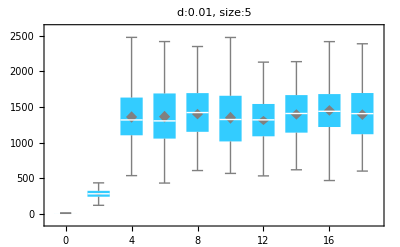

```mathematica
meanTempBox[d1,"d:0.01, size:5"]
```

```mathematica
(**************************************************************************)
```

```mathematica
d2=resultadosR;
```

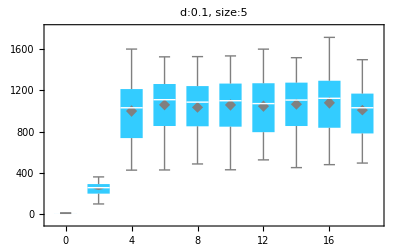

```mathematica
meanTempBox[d2,"d:0.1, size:5"]
```

```mathematica
(**********************************************************************)
```

```mathematica
d3=resultadosR;
```

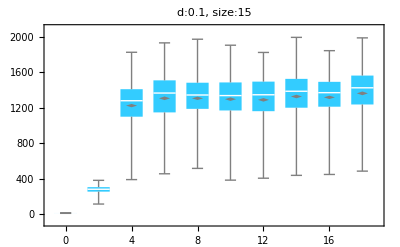

```mathematica
meanTempBox[d3,"d:0.1, size:15"]
```

```mathematica
(*****************************************************************************)
```

```mathematica
d4=resultadosR;
```

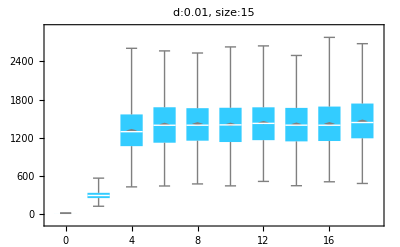

```mathematica
meanTempBox[d4,"d:0.01, size:15"]
```

## References

Yan C - CS, Chepyala SR, Yen C - M, Hsu C - P . Efficient and flexible implementation of Langevin simulation for gene burst production . Sci Rep . 2017; 7 : 16851. doi : 10.1038/s41598 - 017 - 16835 - y